LibraryFunction::strerr: -- Message text not found --

StringSplit::strse: StringSplit[$Failed,\r
] 的位置 1 处应该是字符串或者由字符串组成的列表.

StringSplit::strse: StringSplit[StringSplit[$Failed,\r
],: ,2] 的位置 1 处应该是字符串或者由字符串组成的列表.

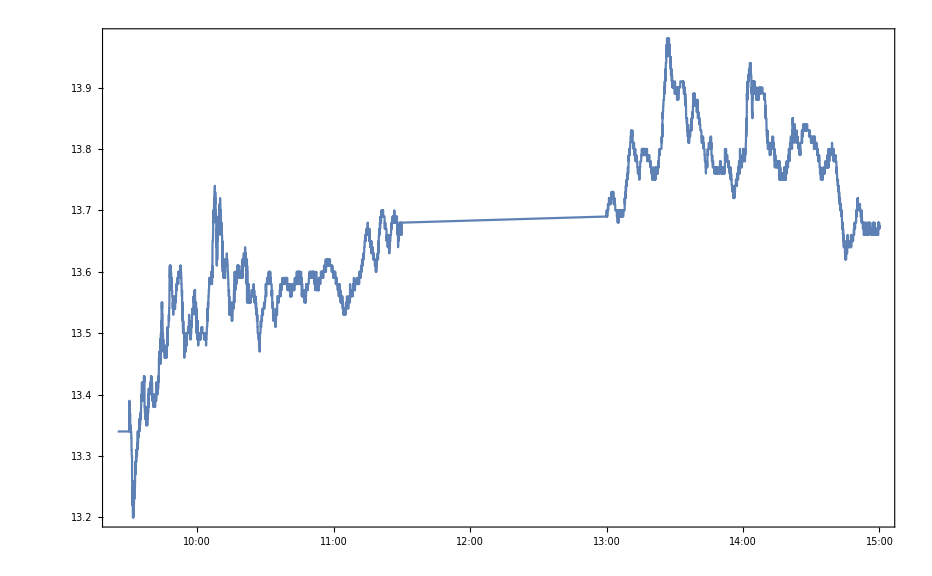

```mathematica
ClearAll["Global`*"]
historyday[date_,stock_]:=Module[{url1,url2,url,data,format,price,time},
url1="http://market.finance.sina.com.cn/downxls.php?date=";
url2="&symbol=sh";
url=url1<>date<>url2<>stock;
data=Import[url,"CSV"];
format=Flatten[StringSplit[#]]&;
data=format/@data;
price=ToExpression/@data[[2;;,2]];
time=data[[2;;,1]];
ts=TimeSeries[price,{time}];
Return[ts];
];
ts=historyday["2017-03-29","600545"];
DateListPlot[ts,PlotTheme->"Detailed"]
```

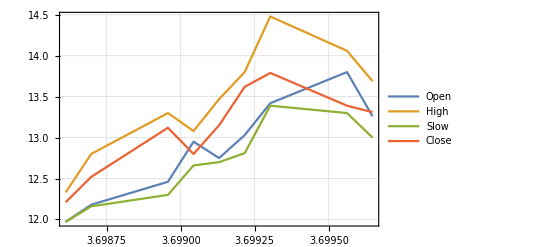

```mathematica
financialfig[stock_,n_]:=Module[{url1,url2,url,data,dataday,dataopen,datahigh,datalow,dataclose,tsopen,tshigh,tslow,tsclose},
url1="http://table.finance.yahoo.com/table.csv?s=";
url2=".ss";
url=url1<>stock<>url2;
data=Import[url,"CSV"];
dataday=data[[2;;n,1]];
dataopen=data[[2;;n,2]];
datahigh=data[[2;;n,3]];
datalow=data[[2;;n,4]];
dataclose=data[[2;;n,5]];
tsopen=TimeSeries[dataopen,{dataday}];
tshigh=TimeSeries[datahigh,{dataday}];
tslow=TimeSeries[datalow,{dataday}];
tsclose=TimeSeries[dataclose,{dataday}];
fig1=DateListPlot[{tsopen,tshigh,tslow,tsclose},PlotLegends->{"Open","High","Slow","Close"},PlotTheme->"Detailed"];
Return[fig1];]
fig1=financialfig["600545",10];
Show[fig1]
```

```mathematica
"
```